January

[07-01-2025]

```mathematica
Sin[Pi/2]
```

1

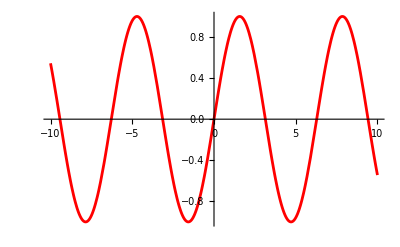

```mathematica
Plot[Sin[x],{x,-10,10},PlotStyle->Red]
```

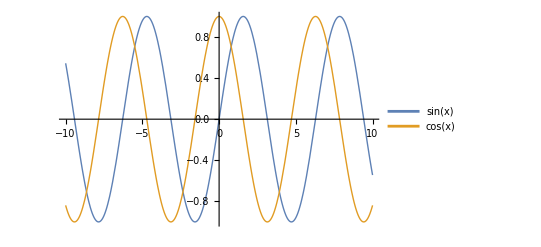

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotStyle->Thick,PlotLegends->"Expressions"]
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotStyle->Thick,PlotLabels->"Expressions"]
```

-Graphics-

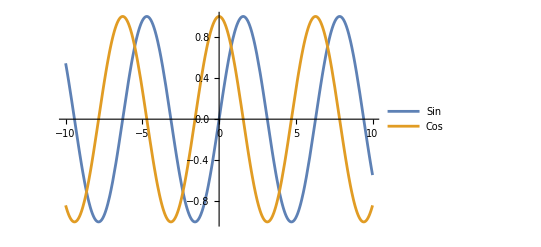

```mathematica
Plot[{Sin[x],Cos[x]},{x,-10,10},PlotLegends->{Sin, Cos}]
```

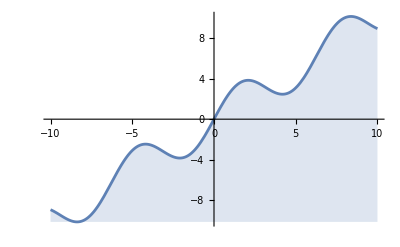

```mathematica
Plot[2Sin[x]+x,{x,-10,10},Filling->Bottom]
```

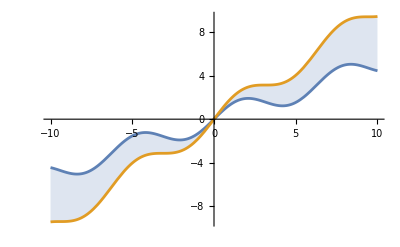

```mathematica
Plot[{Sin[x]+x/2,Sin[x]+x},{x,-10,10},Filling->{1-> {2}}]
```

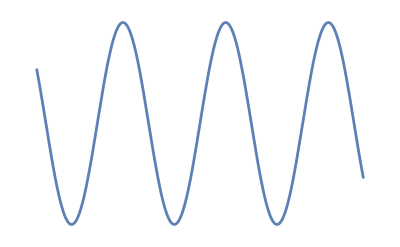

```mathematica
Plot[Sin[x],{x,-10,10},Axes->False]
```

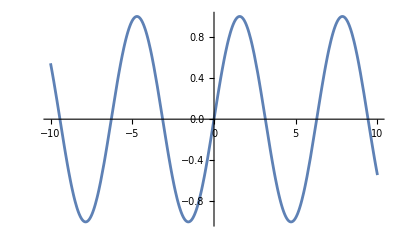

```mathematica
Plot[Sin[x],{x,-10,10},Axes->{True,False}]
```

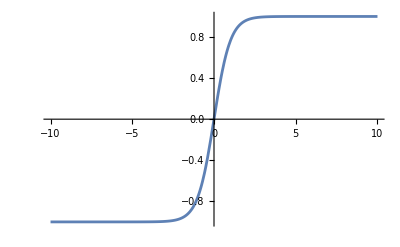

```mathematica
Plot[Tanh[x],{x,-10,10}]
```

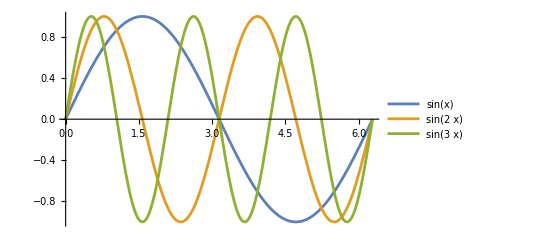

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

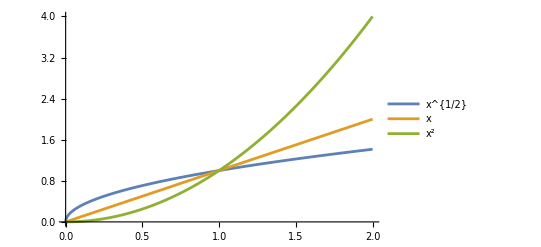

```mathematica
Plot[{x^{1/2},x,x^2},{x,0,2},PlotLegends->"Expressions"]
```

```mathematica
Simplify[Sin[x]Cos[y]+Sin[y]Cos[x]]
```

Sin[x+y]

## Discussion of These Functions (Plot,Table,ListPlot, Manipulate)

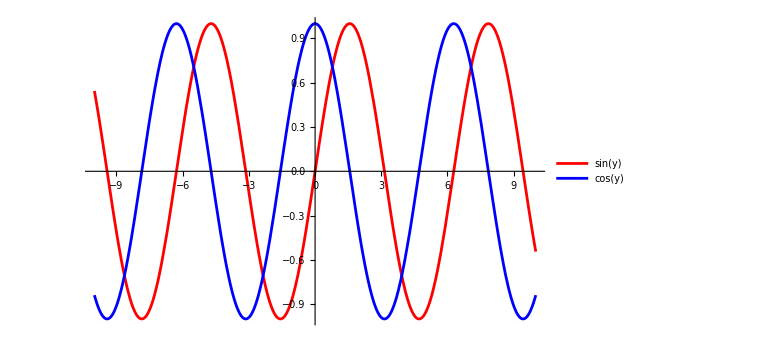

```mathematica
Plot[{Sin[y],Cos[y]},{y,-10,10},PlotStyle->{Red,Blue},PlotLegends->"Expressions",ImageSize->Large,Axes->True]
```

```mathematica
Table[n,{n,1,10}]
```

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[n^2,{n,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[Sin[n*Pi/2],{n, 0,10}]
```

{0,1,0,-1,0,1,0,-1,0,1,0}

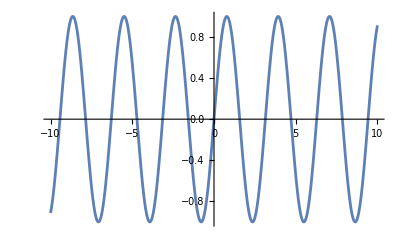
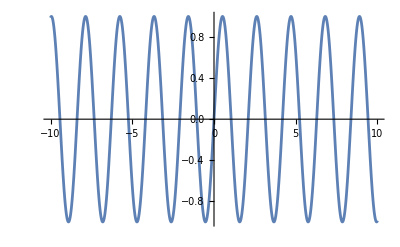
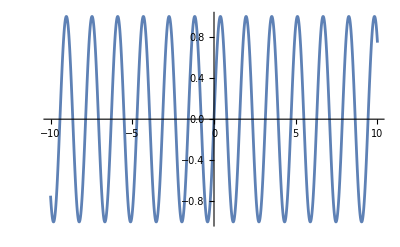
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[Sin[n x],{x,-10,10}],{n,1,4}]
```

```mathematica
factorials = Table[n!,{n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

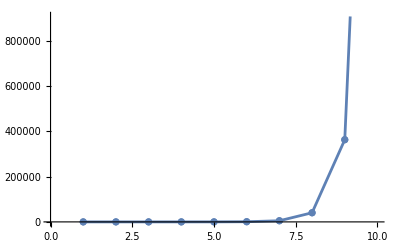

```mathematica
k=ListPlot[factorials,Joined -> True,Mesh->Full]
```

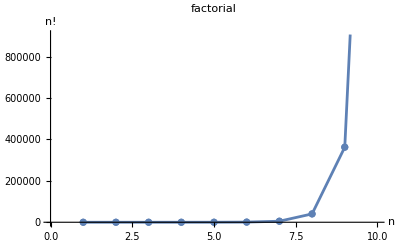

```mathematica
Show[k,AxesLabel->{"n",HoldForm[n!]},PlotLabel->HoldForm[factorial],LabelStyle->{GrayLevel[0.3]}] (*HoldForm prints as the expressionexpr,with expr maintained in an unevaluated form*)
```

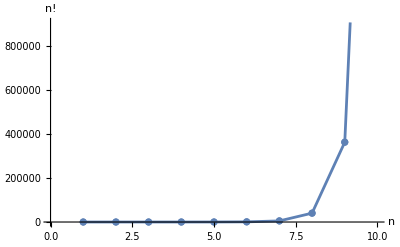

```mathematica
Show[k,AxesLabel->{"n",HoldForm[n!]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",10,GrayLevel[0],Bold}]
```

```mathematica
factorials=Table[Log[n!],{n,1,10}]
```

{0,Log[2],Log[6],Log[24],Log[120],Log[720],Log[5040],Log[40320],Log[362880],Log[3628800]}

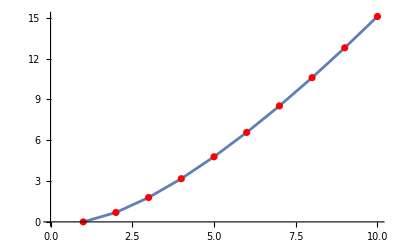

```mathematica
ListPlot[factorials,Joined->True,Mesh->All,MeshStyle->Red]
```

```mathematica
polynomials = Table[n^4,{n,1,10}]
```

{1,16,81,256,625,1296,2401,4096,6561,10000}

```mathematica
exponentials=Table[4^n,{n,1,10}]
```

{4,16,64,256,1024,4096,16384,65536,262144,1048576}

```mathematica
factorials=Table[n!,{n,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

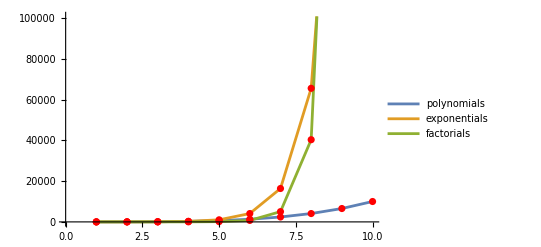

```mathematica
ListPlot[{polynomials,exponentials,factorials},Joined->True,Mesh->All,MeshStyle->{Red},PlotLegends->{"polynomials","exponentials","factorials"}]
```

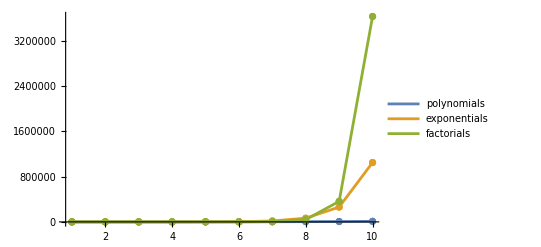

```mathematica
ListPlot[{polynomials,exponentials,factorials},Joined->True,Mesh->Full,PlotLegends->{"polynomials","exponentials","factorials"},PlotRange->Full]
```

```mathematica
Manipulate[n^2,{n,1,10}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,-10,10}],{n,1,10}]
```

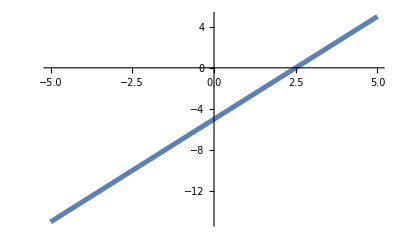

```mathematica
Plot[2x-5,{x,-5,5},PlotStyle->Thickness[0.009]]
```

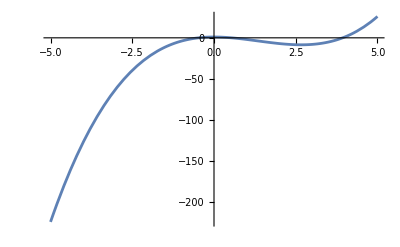

```mathematica
Plot[x^3-4x^2+1,{x,-5,5}]
```

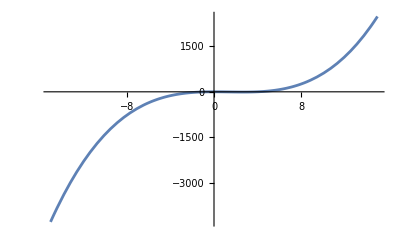

```mathematica
Plot[x^3-4x^2+1,{x,-15,15}]
```

```mathematica
Plot[x^3-4x^2+1,{x,-1,1}]
```

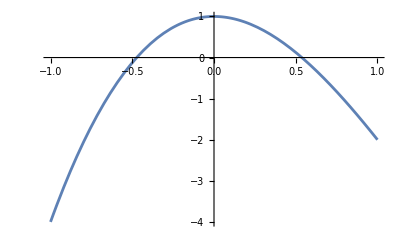

```mathematica
Clear[x]
```

```mathematica
N[Solve[x^3-4 x^2+1==0,x]]
```

{{x→-0.472834},{x→0.537402},{x→3.93543}}

```mathematica
Table[{x,x^3-4x^2+1},{x,0.5,0.6,0.001}];
```

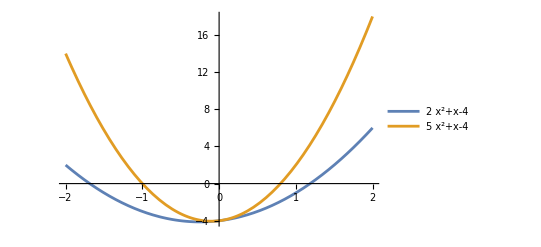

```mathematica
Plot[{2x^2+x-4,5x^2+x-4},{x,-2,2},PlotLegends->"Expressions"]
```

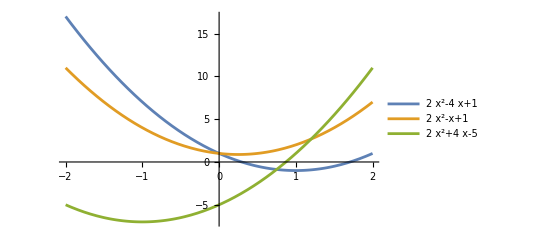

```mathematica
Plot[{2x^2-4x+1,2x^2-x+1,2x^2+4x-5},{x,-2,2},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-5,5},PlotRange->{{-5,5},{-5,5}},Frame->True],{{a,1},-5,5},{{b,0},-5,5},{{c,0},-5,5}]
```

```mathematica
Manipulate[Plot[ {x^2+ x+c},{x,-5,5},PlotRange->{{-5,5},{-10,10}},Frame->True],{c,-5,5}]
```

```mathematica
Manipulate[Plot[ {x^2+ b x+1,(-b/2)^2+b*(-b/2)+1},{x,-5,5},PlotRange->{{-5,5},{-10,10}},Frame->True],{b,-5,5}]
```

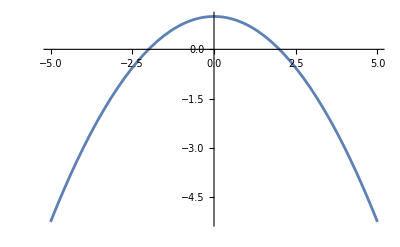

```mathematica
Plot[b^2/4-b^2/2+1,{b,-5,5}]
```

```mathematica
--------Function Behaviour near extrema (Quadratic like behaviour)--------------------
```

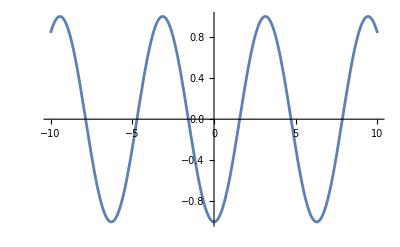

```mathematica
Plot[-Cos[x],{x,-10,10}]
```

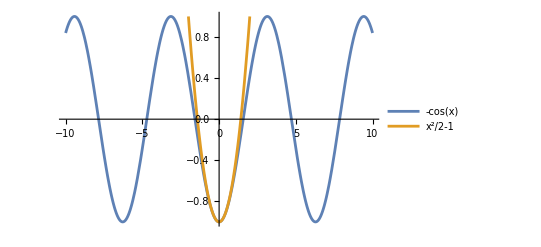

```mathematica
Plot[{-Cos[x],x^2/2-1},{x,-10,10},PlotRange->{-1,1},PlotLegends->"Expressions"]
```

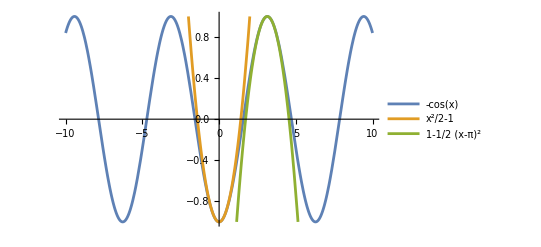

```mathematica
Plot[{-Cos[x],x^2/2-1,1-(x-Pi)^2/2},{x,-10,10},PlotRange->{-1,1},PlotLegends->"Expressions"]
```

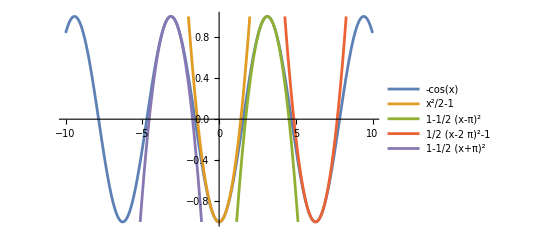

```mathematica
Plot[{-Cos[x],x^2/2-1,1-(x-Pi)^2/2,(x-2*Pi)^2/2-1,1-(x+Pi)^2/2},{x,-10,10},PlotRange->{-1,1},PlotLegends->"Expressions"]
```

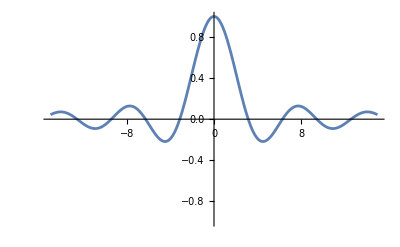

```mathematica
Plot[Sin[x]/x,{x,-15,15},PlotRange->{-1,1}]
```

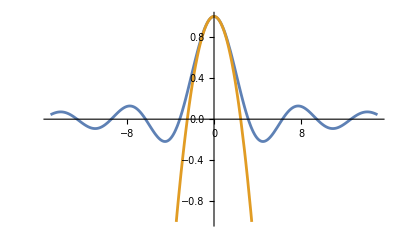

```mathematica
Plot[{Sin[x]/x,1-x^2/6},{x,-15,15},PlotRange->{-1,1}]
```

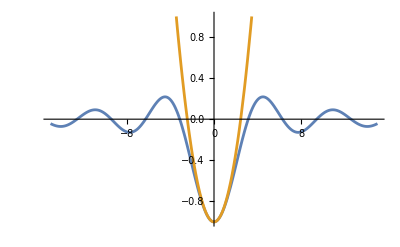

```mathematica
Plot[{(-Sin[x])/x,-1+x^2/6},{x,-15,15},PlotRange->{-1,1}]
```

```mathematica
FindMaximum[(-Sin[x])/x,x]
```

{0.217234,{x→4.49341}}

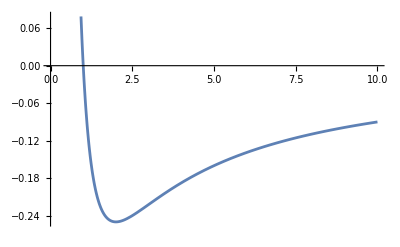

```mathematica
Plot[-1/x+1/x^2,{x,0,10}]
```

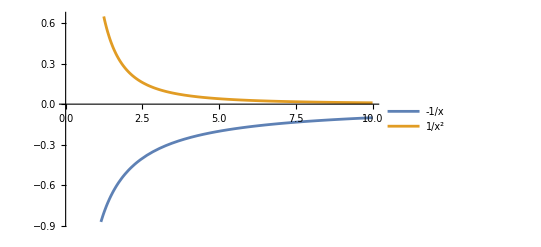

```mathematica
Plot[{-1/x,1/x^2},{x,0,10},PlotLegends->"Expressions"]
```

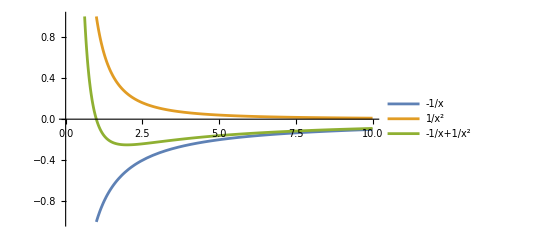

```mathematica
Plot[{-1/x,1/x^2,-1/x+1/x^2},{x,0,10},PlotLegends->"Expressions",PlotRange->{-1,1}]
```

```mathematica
(*To know the zeros of a function*)

Solve[-1/x+1/x^2==0,x]
```

{{x→1}}

```mathematica
FindMinimum[-1/x+1/x^2,x]
```

{-0.25,{x→2.}}

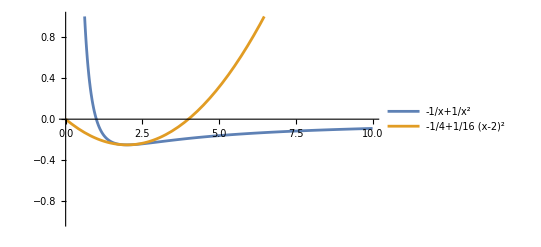

```mathematica
Plot[{-1/x+1/x^2,-1/4+1/16(x-2)^2},{x,0,10},PlotLegends->"Expressions",PlotRange->{-1,1}]
```

```mathematica
FindMinimum[Sin[x]/x,{x,1,10}]
```

{-0.217234,x→4.49341}}

[08-01-2025]

```mathematica
Manipulate[Plot[Sin[n x],{x,-10,10}],{n,1,10}]
```

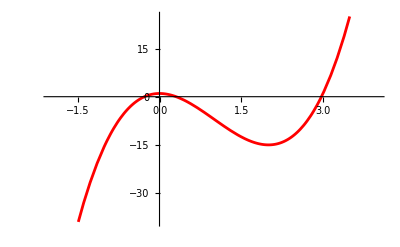

```mathematica
Plot[4x^3-12x^2+1,{x,-2,4}, PlotStyle->Red]
```

```mathematica
Table[{x,x^3-4x^2+1},{x,0.37,0.58,0.00001}];
```

This gives the root approximately. Though all the roots can be solved for, together.

```mathematica
Solve[x^3-4x^2+1==0,x]
```

{{x→},{x→},{x→}}

```mathematica
N[Solve[x^3-4x^2+1==0,x],{Infinity,9}](*{precision, accuracy}*)
```

{{x→-0.47283391},{x→0.53740158},{x→3.93543233}}

HA: Write a C code for Bisection method
/* Program: Finding real roots of nonlinear
   equation using Bisection Method */
#include<stdio.h>
#include<math.h>
#define f(x) 5*x*x*x + 9*x*x + 2*x + 3
float main()
{
   float x0, x1, x2, f0, f1, f2, e;
   int step = 1;
   /* Inputs */
   up:
   printf(“\nEnter two initial guesses:\n”);
   scanf(“%f%f”, &x0, &x1);
   printf(“Enter tolerable error:\n”);
   scanf(“%f”, &e);
   /* Calculating Functional Value */
   f0 = f(x0);
   f1 = f(x1);
   /* Checking whether given guesses brackets the root or not. */
   if( f0 * f1 > 0.0)
   {
      printf(“Incorrect Initial Guesses.\n”);
      goto up;
   }
   /* Implementing Bisection Method */
   printf(“\nStep\t\tx0\t\tx1\t\tx2\t\tf(x2)\n”);
   do
   {
      x2 = (x0 + x1)/2;
      f2 = f(x2);
      printf(“%d\t\t%f\t%f\t%f\t%f\n”,step, x0, x1, x2, f2);
      if( f0 * f2 < 0)
      {
         x1 = x2;
         f1 = f2;
      }
      else
      {
         x0 = x2;
         f0 = f2;
      }
      step = step + 1;
   }while(fabs(f2)>e);
   printf(“\nRoot is: %f”, x2);
}

```mathematica
Plot[{2x^2+x-4,5x^2+x-4},{x,-2,2},PlotLegends->"Expressions"]
```

Higher the coefficient, higher would be the curvature of the curve.

[13-01-2025]
Newton Raphson
-Graphics-

```mathematica
Manipulate[Plot[a x^2+b x+c,{x,-5,5},PlotRange->{{-5,5},{-10,10}},Frame->True],{{a,1},-5,5},{{b,0},-5,5},{{c,0},-5,5}]
```

If a variable is not initialized (as “a” is 1 at the beginning), it starts with the lowest value by default.

>With just c plot just changes its offset.
>When only b varies, the trajectory of minima seems to be parabolic. 
Plotting the function only varying b:
(value of the function at minima)

```mathematica
Manipulate[Plot[ {x^2+b x+1,(-b/2)^2-b*b/2+1},{x,-5,5},Frame->True],{{b,1},-5,5}]
```

# Function behaviour near extrema

```mathematica
Plot[-Cos[x],{x,-10,10}]
```

-Graphics-

Estimating the above as a quadratic function near extrema:
f(x) = -cosx
Taylor series approximation {x0 = 0}
f(x) = 1+(1/2)(x-2)^2

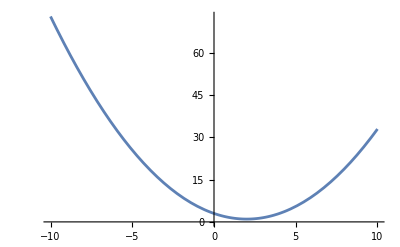

```mathematica
Plot[1+(1/2)(x-2)^2,{x,-10,10}]
```

```mathematica
Plot[{-Cos[x],x^2/2-1,1-(x-Pi)^2/2},{x,-10,10},PlotRange->{-1,1},PlotLegends->"Expressions"]
```

HA: Then find out a generic approximation for any extrema.

```mathematica
Plot[{Sin[x]/x,(x-π)/π^2+1/6 π^3(x-π)^3},{x,0,5},PlotLegends->"Expressions"]
```

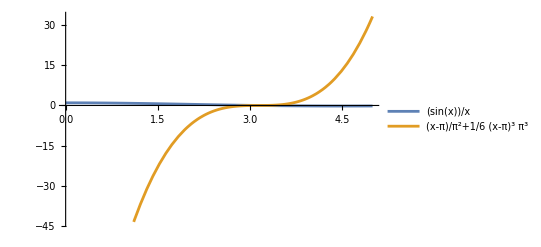

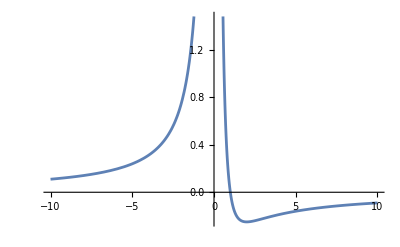

```mathematica
Plot[1/x^2-1/x,{x,-10,10}]
```

[14-01-2025]

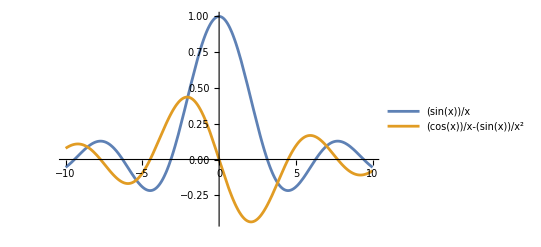

```mathematica
Plot[{Sin[x]/x,Cos[x]/x-Sin[x]/x^2},{x,-10,10},PlotLegends->"Expressions"]
```

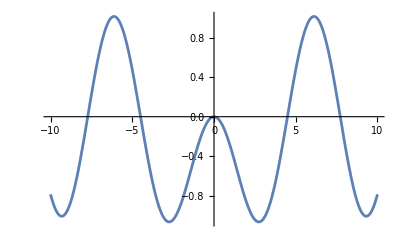

```mathematica
Plot[Cos[x]-Sin[x]/x,{x,-10,10}]
```

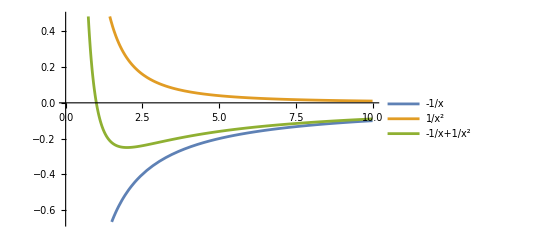

```mathematica
Plot[{-1/x,1/x^2,-1/x+1/x^2},{x,0,10},PlotLegends->"Expressions"]
```

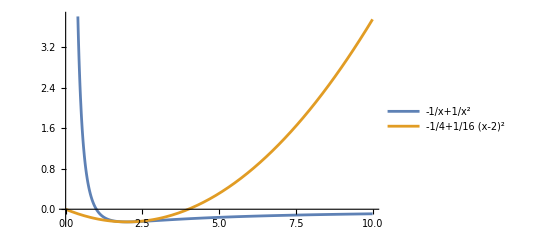

```mathematica
Plot[{-1/x+1/x^2,-1/4+1/16(x-2)^2},{x,0,10},PlotLegends->"Expressions"]
```

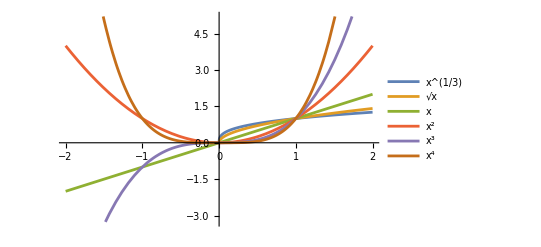

```mathematica
Plot[{x^(1/3),x^(1/2),x,x^2,x^3,x^4},{x,-2,2},PlotLegends->"Expressions"]
```

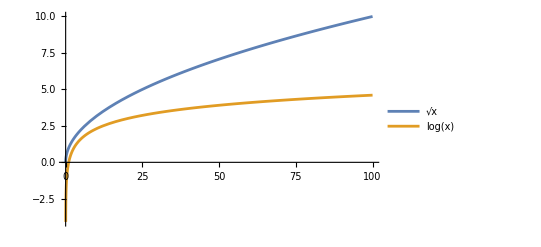

```mathematica
Plot[{x^(1/2),Log[x]},{x,0,100},PlotLegends->"Expressions"]
```

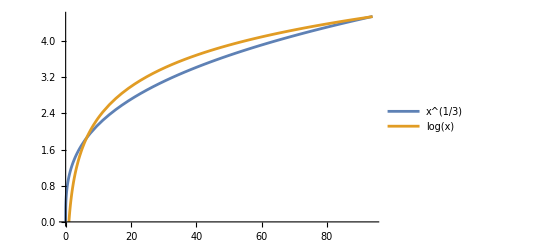

```mathematica
Plot[{x^(1/3),Log[x]},{x,0,94},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[{x^(1/n),Log[x]},{x,0,25},PlotLegends->"Expressions"],{{n,2},1,5}]
```

```mathematica
Manipulate[Plot[{Exp[-x],r-x},{x,-5,5},PlotLegends->"Expressions"],{{r,1},1,5}]
```

[15-01-2025]

Flow in one dimension

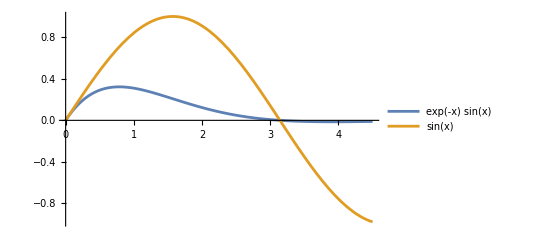

```mathematica
Plot[{Exp[-x]*Sin[x],Sin[x]},{x,0,4.5},PlotRange->Full,PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot[r+x^2,{x,-10,10}],{{r,0},-10,10}]
```

```mathematica
Manipulate[Plot[1+r x+x^2,{x,-5,5},PlotRange->{-10,10}],{{r,0},-5,5}]
```

[20-01-2025]
LC Circuit
C = 100
R = 1
V = 10

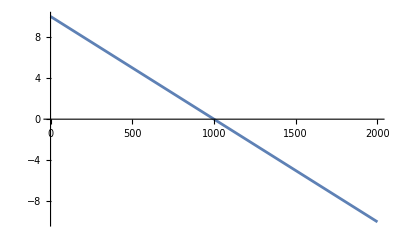

```mathematica
Plot[10-x/100,{x,0,2000}]
```

Turns out that Q = CV = 1000 is a pt of  stable equilibrium. Also we observe that changing R doesn’t affect the stable equilibrium point.

```mathematica
Manipulate[Plot[V/R-x/(R C),{x,0,3000},PlotRange->Full],{V,10,20},{C,100,300},{R,1,5}]
```

Population Growth
Population of a particular species (say bacteria) in an environment (assuming only that exists)
N(t) - Population at time t
r - growth rate
K - carrying capacity

I shall keep x instead of N since N is some predefined object in mathematica.
Simplest model: dN/dt = rN
This suggests  N(t)=N0 exp(rt)
However, there’s a certain carrying capacity above which, the population won’t grow.

Another model [Logistic equation]
dN/dt = rN(1-(N/K))
if N>K rate is negative.

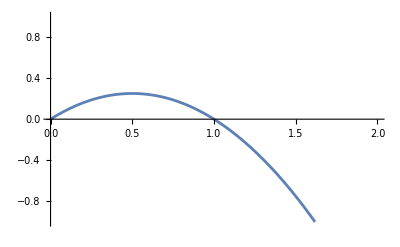

```mathematica
Plot[x (1-x),{x,0,2},PlotRange->{-1,1}]
```

There are two fixed points here as 0 population is also a valid scenario, if you take it as an initial condition, population will never increase. Out of these, N=k is the stable fixed point (of equilibrium) of the system. If N>K, dN/dt is negative.

```mathematica
Manipulate[Plot[r x(1-x/K),{x,0,10},PlotRange->Full],{r,1,2},{K,1,5}]
```

```mathematica
Manipulate[Plot[r -x-Exp[-x],{x,-10,10},PlotRange->{-10,10}],{r,1,20}]
```

```mathematica
Manipulate[Plot[{r -x,Exp[-x]},{x,-10,10},PlotRange->{-10,10}],{{r,0},-20,20}]
```

[21-01-2025]
Giving a pre defined function in the argument of manipulate:

```mathematica
f1=a (1-x);
Manipulate[Plot[f1/.a->a1,{x,0,3}],{a1,0,3}]
```

Properties of a function

```mathematica
Manipulate[Plot[{a^2/(x^2+a^2)},{x,-5,5},PlotRange->Full,PlotLegends->"Lorentzian"],{a,.2,2,.1}]
```

Why increase in a gives increase in the width:

```mathematica
Manipulate[Plot[{Exp[-x^2/a^2]},{x,-5,5},PlotRange->Full,PlotLegends->"Gaussian"],{a,.2,2,.1}]
```

```mathematica
Manipulate[Plot[{Exp[-x^2/a^2],a^2/(x^2+a^2),Exp[-1]},{x,-5,5},PlotRange->Full,PlotLegends->{"Gaussian","Lorentzian","1/e"},PlotLabel->Style["a"->a]],{a,.2,2,.1}]
```

```mathematica
------Vector Plot and Stream Plot Exercise ------
```

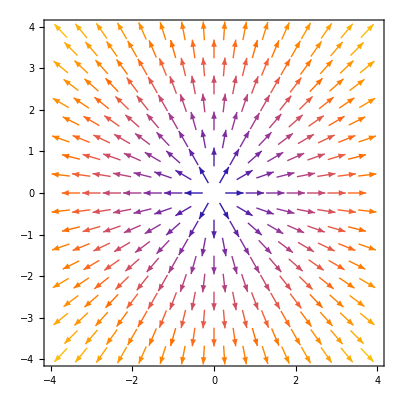

```mathematica
VectorPlot[{x,y},{x,-4,4},{y,-4,4}]
```

```mathematica
Div[{x,y},{x,y}]
```

2

```mathematica
Curl[{x,y},{x,y}]
```

0

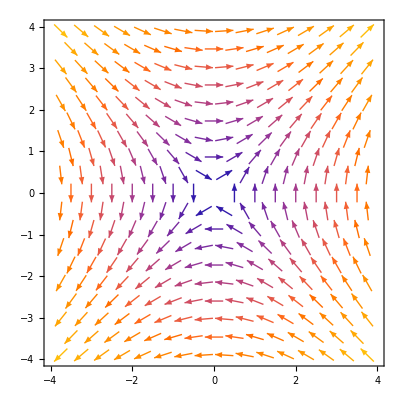

```mathematica
VectorPlot[{y,x},{x,-4,4},{y,-4,4}]
```

```mathematica
Div[{y,x},{x,y}]
```

0

```mathematica
Curl[{y,x},{x,y}]
```

0

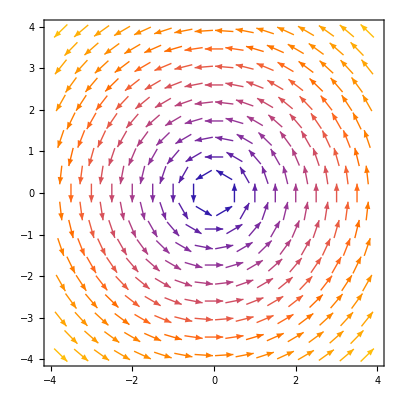

```mathematica
VectorPlot[{-y,x},{x,-4,4},{y,-4,4}]
```

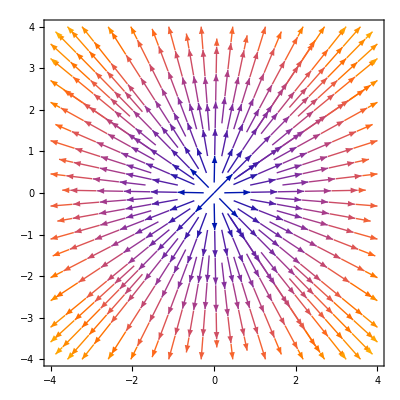

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4}]
```

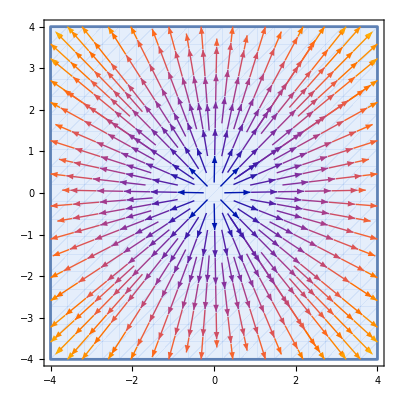

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.05]]
```

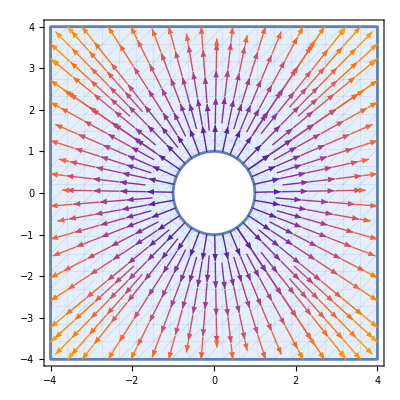

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},n>1]]
```

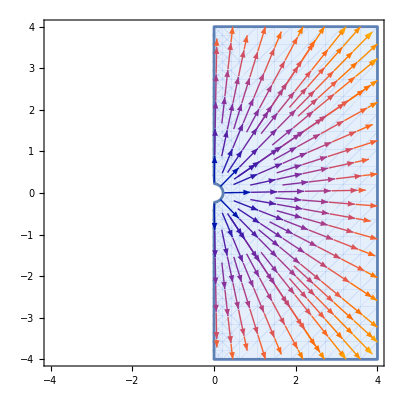

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4},RegionFunction->Function[{x,y,vx,vy,n},vx>0 &&x^2+y^2>0.05]]
```

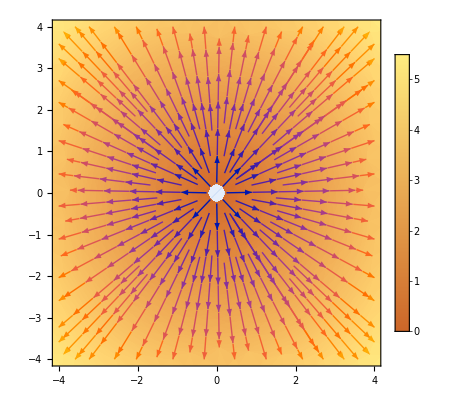

```mathematica
StreamDensityPlot[{x,y},{x,-4,4},{y,-4,4},PlotLegends->Automatic,RegionFunction->Function[{x,y},x^2+y^2>0.05]]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScale->0.06,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Div[{x,y,z},{x,y,z}]
```

3

```mathematica
Curl[{x,y,z},{x,y,z}]
```

{0,0,0}

```mathematica
VectorPlot3D[{-y,x,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScale->0.1,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Electric Field and Potential due to a point charge q, kept at origin
```

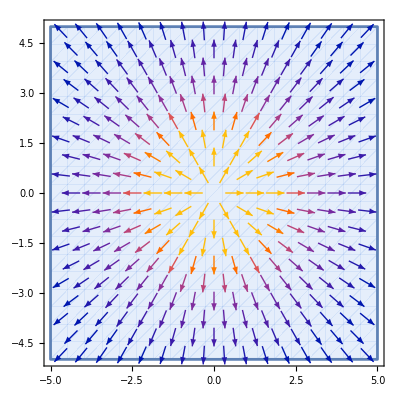

```mathematica
VectorPlot[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,-5,5},{y,-5,5},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.1]]
```

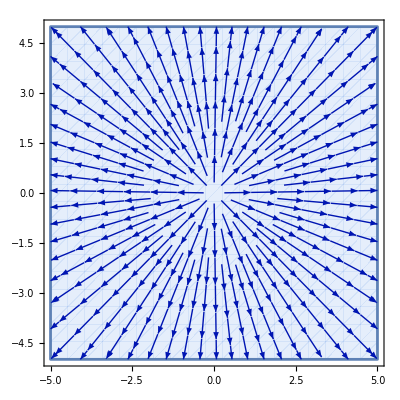

```mathematica
StreamPlot[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,-5,5},{y,-5,5},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.1]]
```

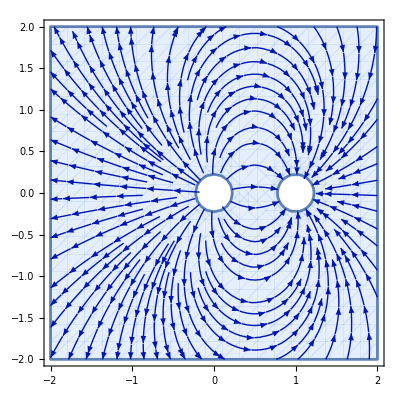

```mathematica
StreamPlot[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy},x^2+y^2>0.05&&(x-1)^2+y^2>0.05]]
```

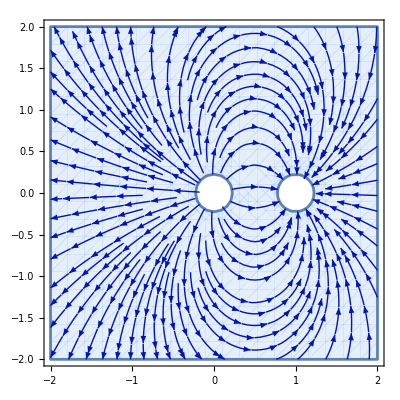

```mathematica
StreamPlot[{x/r^3-(x-1)/r1^3,y/r^3-y/r1^3}/.r->(x^2+y^2)^(1/2) /.r1->((x-1)^2+y^2)^(1/2),{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy},x^2+y^2>0.05&&(x-1)^2+y^2>0.05]]
```

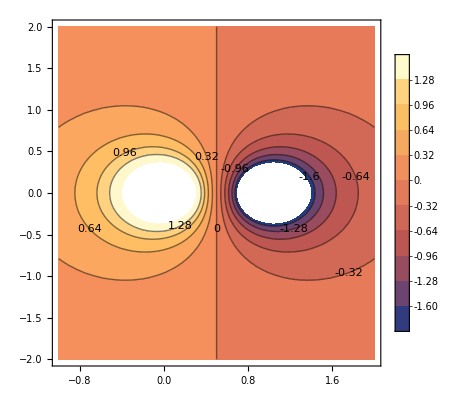

```mathematica
ContourPlot[{1/r-1/r1}/.r->(x^2+y^2)^(1/2) /.r1->((x-1)^2+y^2)^(1/2),{x,-1,2},{y,-2,2},Contours->10,PlotLegends->Automatic,ContourLabels->True]
```

```mathematica
Div[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,y}]
```

-(3 x^2)/((x^2+y^2)^(5/2))-(3 y^2)/((x^2+y^2)^(5/2))+2/((x^2+y^2)^(3/2))

```mathematica
Curl[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,y}]
```

0

```mathematica
Div[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

(3 (-1+x)^2)/(((-1+x)^2+y^2)^(5/2))+(3 y^2)/(((-1+x)^2+y^2)^(5/2))-2/(((-1+x)^2+y^2)^(3/2))-(3 x^2)/((x^2+y^2)^(5/2))-(3 y^2)/((x^2+y^2)^(5/2))+2/((x^2+y^2)^(3/2))

```mathematica
Curl[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

0

```mathematica
VectorPlot[{{x+y,y-x},{y,x+y}},{x,-4,4},{y,-4,4},PlotLayout->"Row"]
```

-Graphics-

```mathematica
Div[{x+y,y-x},{x,y}]
```

2

```mathematica
Curl[{x+y,y-x},{x,y}]
```

-2

```mathematica
Div[{y,x+y},{x,y}]
```

1

```mathematica
Curl[{y,x+y},{x,y}]
```

0

```mathematica
Manipulate[StreamPlot[{(q1  x)/r^3+(q2  (x-1))/r1^3,(q1  y)/r^3+(q2  y)/r1^3}/.r->(x^2+y^2)^(1/2) /.r1->((x-1)^2+y^2)^(1/2),{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2>0.05&&(x-1)^2+y^2>0.05]],{q1,-1,1},{q2,-1,1}]
```

```mathematica
Manipulate[Show[StreamPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],q2]+EX[x,y,Q3[[1]],Q3[[2]],q3],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],q2]+EY[x,y,Q3[[1]],Q3[[2]],q3]},{x,-20,20},{y,-15,15},AspectRatio->.75],Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}]
}],ImageSize->{575,375}],
{{q1,-1},-2,2,.1},
{{q2,2},-2,2,.1},
{{q3,-1},-2,2,.1},{{Q1,{-10,0}}},{{Q2,{0,0}}},{{Q3,{10,0}}},Initialization:>(EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2));EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2)))]
```

```mathematica
Q={1,2}
```

{1,2}

```mathematica
Q[[1]]
```

1

Vector field

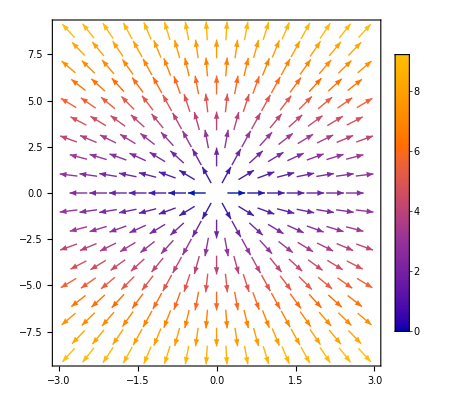

```mathematica
VectorPlot[{x,y},{x,-3,3},{y,-9,9},PlotLegends->Automatic]
```

The divergence is constant:the difference between lines entering and leaving some da is constant throughout.

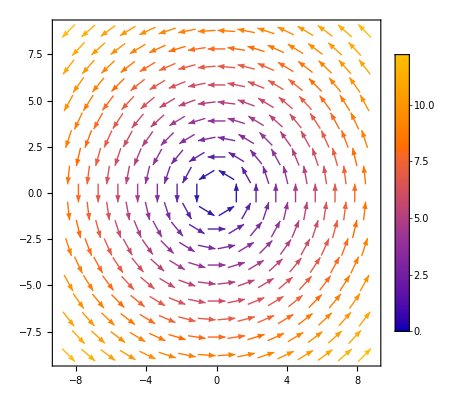

```mathematica
VectorPlot[{-y,x},{x,-9,9},{y,-9,9},PlotLegends->Automatic]
```

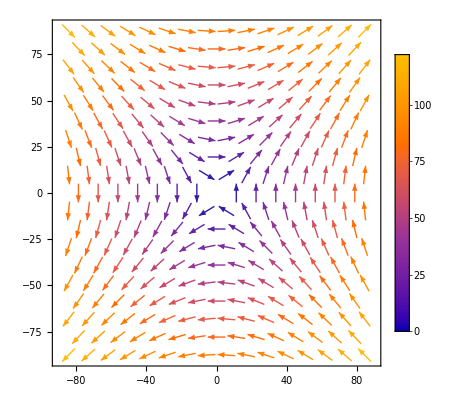

```mathematica
VectorPlot[{y,x},{x,-90,90},{y,-90,90},PlotLegends->Automatic]
```

Lines of stability: all the arrows approach 1 point
Lines of unstability: all the arrows recede 1 point
The origin in this case is called: saddle point (where the above 2 lines seem to meet)

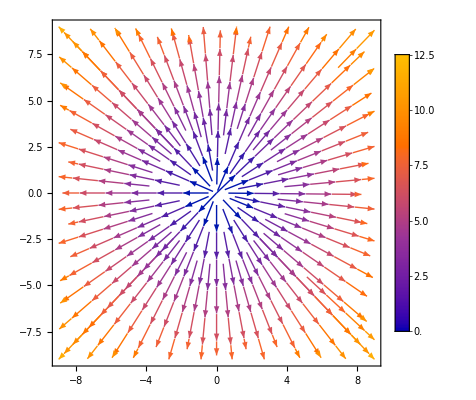

```mathematica
StreamPlot[{x,y},{x,-9,9},{y,-9,9},PlotLegends->Automatic]
```

To remove this numerical unstability at the origin, define a  RegionFunction

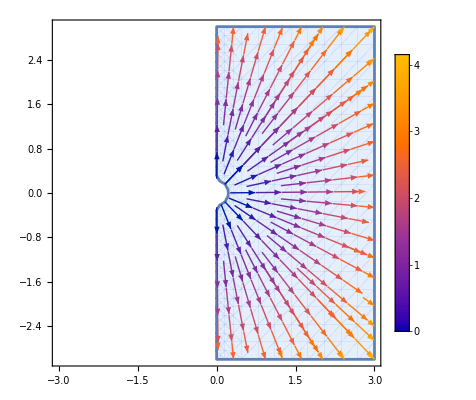

```mathematica
StreamPlot[{x,y},{x,-3,3},{y,-3,3},PlotLegends->Automatic,RegionFunction->Function[{x,y,vx,vy},x^2+y^2>0.05&& vx>0]]
```

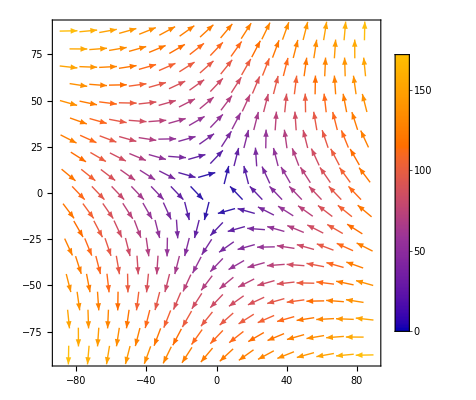

```mathematica
VectorPlot[{y-x,x+y},{x,-90,90},{y,-90,90},PlotLegends->Automatic]
```

```mathematica
VectorPlot3D[{-y,x,z},{x,-3,3},{y,-3,3},{z,-3,3},PlotLegends->Automatic]
```

-Graphics3D-

[22-01-2025]
Let’s go back to Electromagnetism

VectorPlot3D[{x,y,z},{x,-4,4},{y,-4,4},{z,-4,4},PlotLegends->Automatic,VectorScale->0.09]
-Graphics3D-
VectorPlot3D[{-y,x,z},{x,-4,4},{y,-4,4},{z,-1,1},PlotLegends->Automatic,VectorScale->0.1,AxesLabel->{"x","y","z"}]
-Graphics3D-
D == Div[{-y,x,z},{x,y,z}]
C ==Curl[{-y,x,z},{x,y,z}]
D==1
C=={0,0,2}

Electric field due to a point charge situated at the origin.

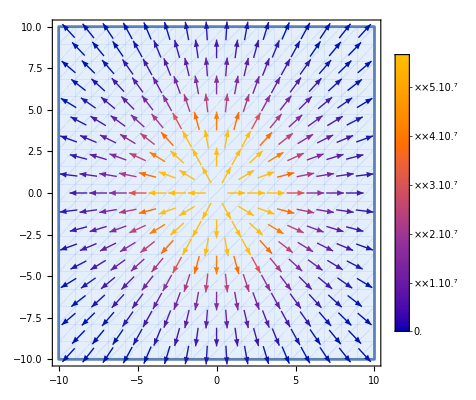
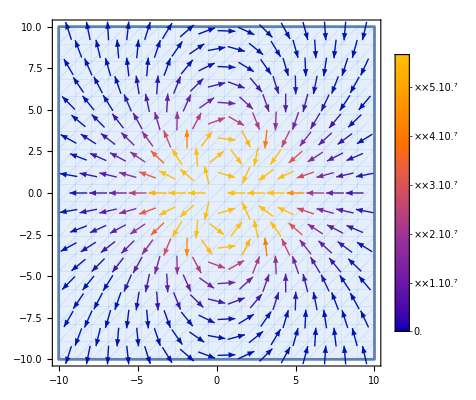
VectorPlot[{x/((x^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))},{x,-10,10},{y,-10,10},RegionFunction->Function[{x,y},x^2+y^2>0.2],PlotLegends->Automatic]

-Graphics-

VectorPlot[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,-10,10},{y,-10,10},RegionFunction->Function[{x,y},x^2+y^2>0.2],PlotLegends->Automatic]
-Graphics-

Manipulate[StreamPlot[{(q1 x)/((x^2+y^2)^(3/2))+(q2 (x-1))/(((x-1)^2+y^2)^(3/2)),(q1 y)/((x^2+y^2)^(3/2))+(q2 y)/(((x-1)^2+y^2)^(3/2))},{x,-10,10},{y,-10,10},PlotLegends->Automatic,],{q1,-10,10},{q2,-10,10}]

Curl and divergence

```mathematica
Curl[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

0

```mathematica
Div[{x/((x^2+y^2)^(3/2))-(x-1)/(((x-1)^2+y^2)^(3/2)),y/((x^2+y^2)^(3/2))-y/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

(3 (-1+x)^2)/(((-1+x)^2+y^2)^(5/2))+(3 y^2)/(((-1+x)^2+y^2)^(5/2))-2/(((-1+x)^2+y^2)^(3/2))-(3 x^2)/((x^2+y^2)^(5/2))-(3 y^2)/((x^2+y^2)^(5/2))+2/((x^2+y^2)^(3/2))

Looks interesting folks! The above is for unit positive and negative charges. Following is a generic divergence:

```mathematica
Div[{(q1 x)/((x^2+y^2)^(3/2))+(q2 (x-1))/(((x-1)^2+y^2)^(3/2)),(q1 y)/((x^2+y^2)^(3/2))+(q2 y)/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

-(3 q2 (-1+x)^2)/(((-1+x)^2+y^2)^(5/2))-(3 q2 y^2)/(((-1+x)^2+y^2)^(5/2))+(2 q2)/(((-1+x)^2+y^2)^(3/2))-(3 q1 x^2)/((x^2+y^2)^(5/2))-(3 q1 y^2)/((x^2+y^2)^(5/2))+(2 q1)/((x^2+y^2)^(3/2))

```mathematica
Curl[{(q1 x)/((x^2+y^2)^(3/2))+(q2 (x-1))/(((x-1)^2+y^2)^(3/2)),(q1 y)/((x^2+y^2)^(3/2))+(q2 y)/(((x-1)^2+y^2)^(3/2))},{x,y}]
```

0

Three charge system

```mathematica
Manipulate[Show[StreamPlot[{EX[x,y,Q1[[1]],Q1[[2]],q1]+EX[x,y,Q2[[1]],Q2[[2]],q2]+EX[x,y,Q3[[1]],Q3[[2]],q3],EY[x,y,Q1[[1]],Q1[[2]],q1]+EY[x,y,Q2[[1]],Q2[[2]],q2]+EY[x,y,Q3[[1]],Q3[[2]],q3]},{x,-20,20},{y,-15,15},AspectRatio->.75],Graphics[{RGBColor[{Boole[q1<0],0,0}],Circle[{Q1[[1]],Q1[[2]]},1.25],Text[Style[N[q1],10,Bold],{Q1[[1]],Q1[[2]]}],RGBColor[{Boole[q2<0],0,0}],Circle[{Q2[[1]],Q2[[2]]},1.25],Text[Style[N[q2],10,Bold],{Q2[[1]],Q2[[2]]}],RGBColor[{Boole[q3<0],0,0}],Circle[{Q3[[1]],Q3[[2]]},1.25],Text[Style[N[q3],10,Bold],{Q3[[1]],Q3[[2]]}]
}],ImageSize->{575,375}],
{{q1,-1},-2,2,.1},
{{q2,2},-2,2,.1},
{{q3,-1},-2,2,.1},{{Q1,{-10,0}}},{{Q2,{0,0}}},{{Q3,{10,0}}},Initialization:>(EX[x_,y_,xq_,yq_,qn_]:=((x-xq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2));EY[x_,y_,xq_,yq_,qn_]:=((y-yq) qn)/(((x-xq)^2+(y-yq)^2)^(3/2)))]

Manipulate[StreamPlot[{(q1 x)/((x^2+y^2)^(3/2))+(q2 (x-10))/(((x-10)^2+y^2)^(3/2))+(q3 (x+10))/(((x+10)^2+y^2)^(3/2)),(q1 y)/((x^2+y^2)^(3/2))+(q2 y)/(((x-10)^2+y^2)^(3/2))+(q3 y)/(((x+10)^2+y^2)^(3/2))},{x,-10,10},{y,-10,10},PlotLegends->Automatic],{q1,-10,10},{q2,-10,10},{q3,-10,10}]
```

[27-01-2025]
Simple harmonic oscillation
d^2[x]/dt^2 = -ω^2x
Ansatz:
x = Acos(ωt) + Bsin(ωt)
or
x = Acos(ωt + ϕ)
or
x = Asin(ωt + ϕ)

```mathematica
Manipulate[Plot[A Cos[ω t + ϕ],{t,-10,10}],{A,0,5},{ω,0,5},{ϕ,-Pi,Pi}]
```

## Spring mass system

```mathematica
Manipulate[Plot[{Cos[ω t]+Sin[ω t], Cos[ω t + ϕ], Sin[ω t+ϕ]},{t,-10,10},PlotLegends->{"Cos[ω t]+Sin[ω t]"," Cos[ω t + ϕ]", "Sin[ω t + ϕ]"}],{t,-5,5},{ω,-2,2},{ϕ,-Pi,Pi}]
```

Find a range of angles for which the latter two overlap.

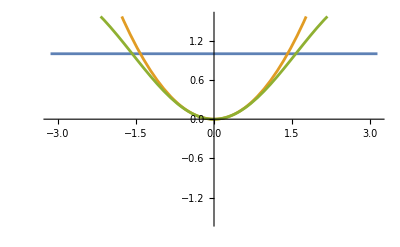

```mathematica
Plot[{1,(theta^2)/2, 1- Cos[theta]},{theta,-3.14,3.14},PlotRange->{-1.57,1.57}]
```

If Ṽ(θ)=1, it’s the total energy of the system !

[28-01-2025]
Non Dimensionalisation

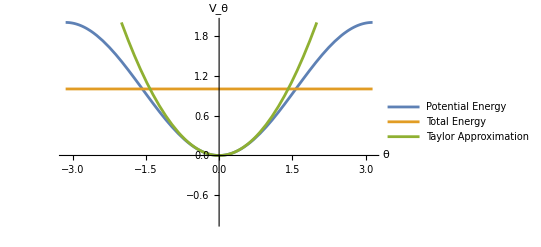

```mathematica
Plot[{1-Cos[θ],1,θ^2/2},{θ,-Pi,Pi},PlotRange->{-1,2},AxesLabel->{Style[θ,16],Style[Subscript[V, θ],16]},AxesStyle->Thick,PlotLegends->{"Potential Energy","Total Energy","Taylor Approximation"} ]
```

\[KernelIcon]To get the decimal value of the following:

```mathematica
Solve[a==1/√2,a]//N
```

{{a→0.707107}}

```mathematica
Manipulate[Plot[{-γ/Cos[θ]^2 x^2 +Tan[θ] x +1,-Tan[ϕ] x +1},{x,0,10},PlotRange->{-5,5}],{θ,0,Pi/2},{ϕ,0,Pi/2},{γ,0,1}]
```

[29-01-2025]
Non-dimensionalisation
Parametric plot: a built-in function

```mathematica
Manipulate[ParametricPlot[{{0.1 t Cos[ω t],0.1 t Sin[ω t]},{0.1 t Cos[2 ω t],0.1 t Sin[2 ω t]}},{t,0,20}],{{ω,2},1,10}]
```

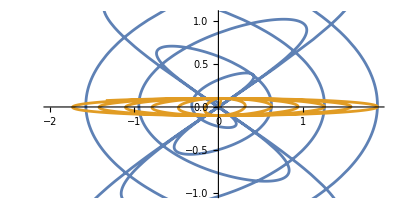

```mathematica
ParametricPlot[{{0.1 t Cos[3 t],0.1 t Sin[2 t]},{0.1 t Cos[2t],0.1  Sin[2 t]}},{t,0,20}]
```

What happens if u and ω are changed?
The plot WOULD change! Since that information is buried in X,Y and Z [See notes for the context SNC]

Mathematica’s calculus commands:

```mathematica
D[Log[x],x]
```

1/x

```mathematica
D[Log[x],{x,3}]
```

2/x^3

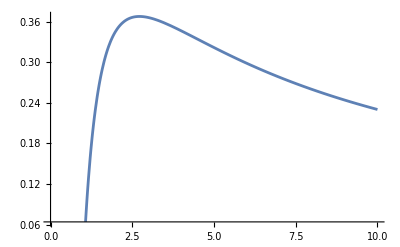

```mathematica
Plot[Log[x]/x,{x,0,10}]
```

```mathematica
soLog=Solve[D[Log[x]/x,x]==0,x]
```

{{x→ⅇ}}

This is the value of x where we have the maximum. There are 2 brackets for a reason.

```mathematica
Solve[D[Log[x]/x,x]==0,x]//N
```

{{x→2.71828}}

Another [this time redundant] way of taking a derivative:

```mathematica
sol3 = D[Log[x]/x,x]
```

1/x^2-Log[x]/x^2

```mathematica
D[sol3,x]
```

0

```mathematica
sol = Solve[2 x^2+2 x -1 == 0,x]
```

{{x→1/2 (-1-√3)},{x→1/2 (-1+√3)}}

```mathematica
sol[[1]]
```

{x→1/2 (-1-√3)}

Putting roots in y = x

```mathematica
x/.sol[[1]]
```

1/2 (-1-√3)

To get multiple roots, and substitute back into the equation, you need to define a function.

```mathematica
2 x^2 +2 x - 1/.sol[[1]]//N
```

0.

```mathematica
x/.sol
```

{1/2 (-1-√3),1/2 (-1+√3)}

Just a different function:

```mathematica
sol1 = Solve[2 x^3+2 x^2 -x == 0,x]
x/.sol
x/.sol//N
```

{{x→0},{x→1/2 (-1-√3)},{x→1/2 (-1+√3)}}

{1/2 (-1-√3),1/2 (-1+√3)}

{-1.36603,0.366025}

HA: Check if it’s a maximum or a minimum.

```mathematica
logs=Solve[D[Log[x]/x,x]==0,x]
sol4=D[Log[x]/x,{x,2}]
sol4/.logs[[1]]
(*Bingo! Maximum*)
```

{{x→ⅇ}}

-3/x^3+(2 Log[x])/x^3

-1/ⅇ^3